```mathematica
n = Pi
```

π

```mathematica
A = 1
```

1

```mathematica
B = 1
```

1

```mathematica
a = 1
```

1

```mathematica
b = 1
```

1

```mathematica
h1 = 0.1
h2 = 0.1
```

0.1

0.1

```mathematica
trueSol = Table[((A Sinh[(Pi(a-x))/b])/Sinh[(Pi a)/b] Sin[Pi y/b] + B * Sinh[(Pi (b-y))/a]/Sinh[(Pi b)/a]* Sin[(Pi x)/a]/.x->i h1 /. y->j h2),{i,0,1/h1},{j,0,1/h2}]
```

{{0.,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.22465×10^-16},{0.309017,0.450675,0.592699,0.709095,0.7796,0.790785,0.736718,0.619063,0.446558,0.233883,8.93022×10^-17},{0.587785,0.592699,0.624204,0.656215,0.66873,0.648106,0.587162,0.484963,0.346227,0.180335,6.50262×10^-17},{0.809017,0.709095,0.656215,0.623896,0.592083,0.5468,0.479815,0.388188,0.273612,0.141525,4.7221×10^-17},{0.951057,0.7796,0.66873,0.592083,0.529868,0.468084,0.39789,0.314993,0.218954,0.112382,3.41148×10^-17},{1.,0.790785,0.648106,0.5468,0.468084,0.398537,0.329313,0.25545,0.175184,0.0892299,2.44033×10^-17},{0.951057,0.736718,0.587162,0.479815,0.39789,0.329313,0.265911,0.202725,0.137386,0.0694991,1.71203×10^-17},{0.809017,0.619063,0.484963,0.388188,0.314993,0.25545,0.202725,0.152481,0.102361,0.0514927,1.15409×10^-17},{0.587785,0.446558,0.346227,0.273612,0.218954,0.175184,0.137386,0.102361,0.06825,0.0341944,7.10992×10^-18},{0.309017,0.233883,0.180335,0.141525,0.112382,0.0892299,0.0694991,0.0514927,0.0341944,0.0170902,3.38647×10^-18},{1.22465×10^-16,8.93022×10^-17,6.50262×10^-17,4.7221×10^-17,3.41148×10^-17,2.44033×10^-17,1.71203×10^-17,1.15409×10^-17,7.10992×10^-18,3.38647×10^-18,0.}}

```mathematica
Table[{i,j},{i,0,1/h1},{j,0,1/h2}]//MatrixForm
```

((0
0) | (0
1) | (0
2) | (0
3) | (0
4) | (0
5) | (0
6) | (0
7) | (0
8) | (0
9) | (0
10)
(1
0) | (1
1) | (1
2) | (1
3) | (1
4) | (1
5) | (1
6) | (1
7) | (1
8) | (1
9) | (1
10)
(2
0) | (2
1) | (2
2) | (2
3) | (2
4) | (2
5) | (2
6) | (2
7) | (2
8) | (2
9) | (2
10)
(3
0) | (3
1) | (3
2) | (3
3) | (3
4) | (3
5) | (3
6) | (3
7) | (3
8) | (3
9) | (3
10)
(4
0) | (4
1) | (4
2) | (4
3) | (4
4) | (4
5) | (4
6) | (4
7) | (4
8) | (4
9) | (4
10)
(5
0) | (5
1) | (5
2) | (5
3) | (5
4) | (5
5) | (5
6) | (5
7) | (5
8) | (5
9) | (5
10)
(6
0) | (6
1) | (6
2) | (6
3) | (6
4) | (6
5) | (6
6) | (6
7) | (6
8) | (6
9) | (6
10)
(7
0) | (7
1) | (7
2) | (7
3) | (7
4) | (7
5) | (7
6) | (7
7) | (7
8) | (7
9) | (7
10)
(8
0) | (8
1) | (8
2) | (8
3) | (8
4) | (8
5) | (8
6) | (8
7) | (8
8) | (8
9) | (8
10)
(9
0) | (9
1) | (9
2) | (9
3) | (9
4) | (9
5) | (9
6) | (9
7) | (9
8) | (9
9) | (9
10)
(10
0) | (10
1) | (10
2) | (10
3) | (10
4) | (10
5) | (10
6) | (10
7) | (10
8) | (10
9) | (10
10))

```mathematica
Laplacian[A/Sinh[(n a)/b] Sinh[(n(a-x))/b]Sin[(a y)/b] + 1/Sinh[(n b)/a] Sinh[(n(b-y))/a]Sin[(n x)/b],{x,y}]//FullSimplify
```

(-1+π^2) Csch[π] Sin[y] Sinh[π-π x]

```mathematica
SetDirectory[NotebookDirectory[]]


MatrixPlot
```

C:\Users\mouze\Desktop\CM_labs\lab9\lab9\lab9

MatrixPlot

```mathematica
matrixNum = Import["test.txt","Table"]
```

{{0,0.309017,0.587785,0.809017,0.951057,1,0.951057,0.809017,0.587785,0.309017,0},{0.309017,0.451796,0.594576,0.711435,0.782153,0.793323,0.739034,0.620976,0.447921,0.234591,0},{0.587785,0.594576,0.627288,0.659998,0.6728,0.652107,0.590782,0.487934,0.348334,0.181428,0},{0.809017,0.711435,0.659998,0.628469,0.596939,0.551522,0.484051,0.391642,0.276052,0.142786,0},{0.951057,0.782153,0.6728,0.596939,0.534966,0.472992,0.402258,0.318533,0.221443,0.113666,0},{1,0.793323,0.652107,0.551522,0.472992,0.403224,0.333455,0.258789,0.177523,0.0904339,0},{0.951057,0.739034,0.590782,0.484051,0.402258,0.333455,0.26955,0.205645,0.139426,0.0705466,0},{0.809017,0.620976,0.487934,0.391642,0.318533,0.258789,0.205645,0.154816,0.103987,0.0523269,0},{0.587785,0.447921,0.348334,0.276052,0.221443,0.177523,0.139426,0.103987,0.0693804,0.0347735,0},{0.309017,0.234591,0.181428,0.142786,0.113666,0.0904339,0.0705466,0.0523269,0.0347735,0.0173868,0},{-2.06379×10^-13,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Animate[Show[ListPlot[matrixNum[[IntegerPart@y]],Joined->True], ListPlot[trueSol[[IntegerPart@y]],Joined->True,PlotStyle->{Orange,Dashed}],ImageSize->500],{y,1,Length@matrixNum}]
```

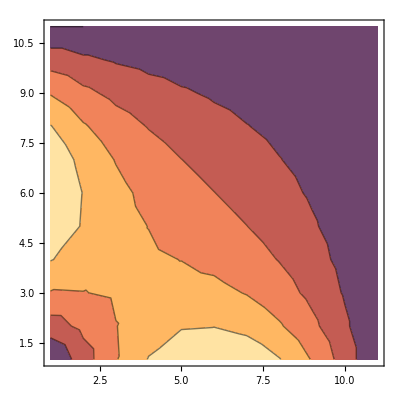

```mathematica
Show[ListContourPlot[matrixNum]]
```